```mathematica
vars={{},{},5,100};(*{Ds,Phis,m,tmax}*)
{th,tl,Jh,Jl}=Sqrt[{0.1,0.1,0.05,0.1}];
{kappa,gamma}={0.1,0.1};
(*Erbeta=20;beta=40*)
Edotr=0.1;(*10^6*ev/cm * 5nm*)
beta=20;(*beta=40 for Temp=0.025; for 300K*)
Erbeta=Edotr*beta;
Print["Erbeta = ",Erbeta];
```

Erbeta = 2.

```mathematica
ntraj=50;
maxiter=100;
current={};
gs=Range[0.01,1,0.1];(*{0.05,0.1,0.5,1,2}*);
res={};allout={};
Do[
Print["================= gg = ",gg,"================="];
alloutx={};
Do[
If[Mod[itraj,10]==0,Print[" traj = ",itraj]];
out=trajectory4[5,vars,gg,th,tl,Jh,Jl,kappa,gamma,maxiter];
AppendTo[alloutx,out];
,{itraj,1,ntraj}];
AppendTo[allout,alloutx];
,{gg,gs}];
```

================= gg = 0.01=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.11=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.21=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.31=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.41=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.51=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.61=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.71=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.81=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

================= gg = 0.91=================

traj = 10

traj = 20

traj = 30

traj = 40

traj = 50

```mathematica
(*Export["/Users/panda/repos/transport-code/OUT.csv",allout]*)
```

/Users/panda/repos/transport-code/OUT.csv

```mathematica
totrates=Table[r[j],{j,1,26}];
slist=Insert[Accumulate[totrates],0,1];
ltotr=26;(*Length[totrates];*)
R= Total[totrates];

(* time increment *)
u=RandomReal[{0,1}];
dt = (-1/R )*Log[u];
t += dt;
AppendTo[times,t];
```

```mathematica
currents9to24={1,1,-1,-1,-1,-1,1,1,-1,1,-1,1,1,-1,1,-1};
Gettpm[totrates_]:=Module[{slist,ltotr,R,u,dt,slist1,slist2,len,R1,R2,rate1,rate2,dt1,dt2},
rate1=Table[totrates[[i]],{i,{1,2,7,8,10,12,13,15}}];
rate2=Table[totrates[[i]],{i,{3,4,5,6,9,11,14,16}}];
slist1=Insert[Accumulate[rate1],0,1];
slist2=Insert[Accumulate[rate2],0,1];
len=8;
R1= slist1[[-1]];
R2= slist2[[-1]];
dt1 = (1/R1 )*Log[1/RandomReal[{10^-10,1}]];
dt2 = (1/R1 )*Log[1/RandomReal[{10^-10,1}]];
{dt1,dt2}
];


Gett2[totrates_]:=Module[{slist,ltotr,R,u,dt},
slist=Insert[Accumulate[totrates],0,1];
ltotr=Length[totrates];(*Length[totrates];*)
R= slist[[-1]];(*Total[totrates];*)
u=RandomReal[{10^-10,1}];
dt = (1/R )*Log[1/u];
dt
];

Gett3[totrates_]:=Module[{slist,ltotr,R,u,dt},
1/Total[totrates]];
```

```mathematica
nav=5;
ntraj=50;
maxiter=100;
current={};
gs=Range[0.01,1,0.1];(*{0.05,0.1,0.5,1,2}*);
ig=0;
Is={};Ivsg={};Ivsg2={};Ivsg2s={};
charg={};tms={};rc={};times12={};
Do[
ig+=1;
alloutx=allout[[ig]];
Ix={};chargx={};Ix2={};
tm=0;rcx={};
Do[

{out2,Evst}=alloutx[[itraj]];
charges=out2[[All,3]];
tottime=out2[[-1,2]];
AppendTo[Ix,Total[charges]/tottime];

rates=out2[[All,10]];
tottime2=0;
xx=rates[[All,9;;24]];

Do[
dts=Gett2/@xx;
tottime2+=Total[dts];
,{ii,1,nav}];
tottime2=tottime2/nav;

(*If[itraj==1,times12x =Gettpm/@xx];
times12x +=Gettpm/@xx;
*)
AppendTo[rcx,Total[Total[xx]]];

AppendTo[Ix2,Total[charges]/tottime2];
AppendTo[chargx,Total[charges]];

tm +=tottime2;
,{itraj,1,ntraj}];

tm=tm/ntraj;

(*AppendTo[times12,times12x/ntraj];*)
AppendTo[rc,Total[rcx]];
AppendTo[tms,{gg,tm}];
AppendTo[Is,Ix];
AppendTo[Ivsg,{gg,Total[Ix]}];
AppendTo[Ivsg2,{gg,Total[Ix2]}];
AppendTo[Ivsg2s,Ix2];
AppendTo[charg,{gg,Total[chargx]}];
,{gg,gs}];
```

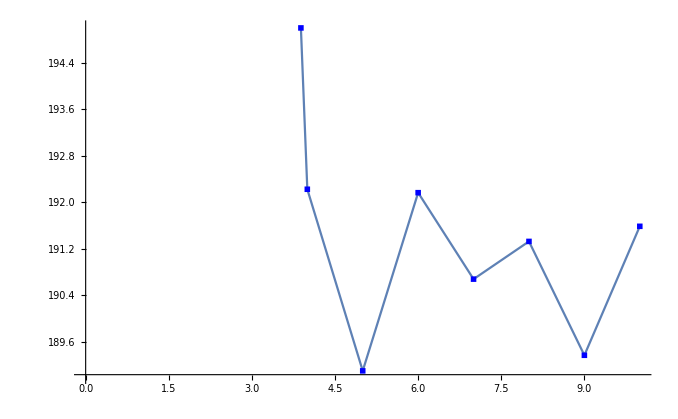

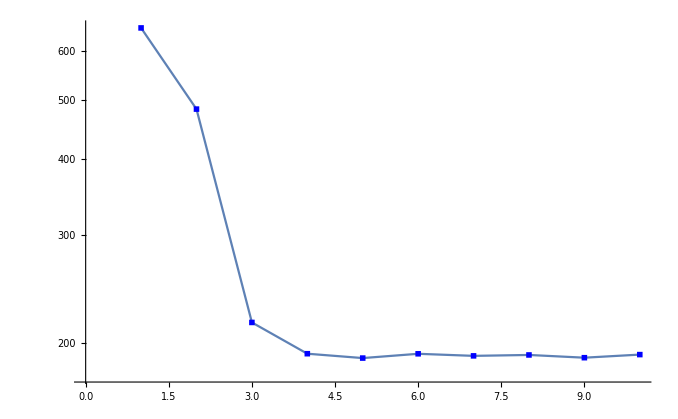

```mathematica
ListPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue],PlotRange->{189,195}]
ListLogPlot[rc,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

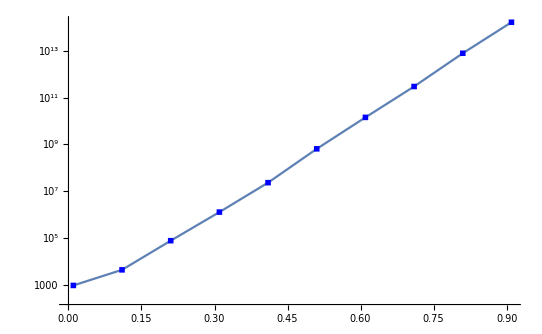

```mathematica
ListLogPlot[tms,Joined->True,PlotMarkers->Style["■", Small, Blue]]
```

```mathematica
tms
```

{{0.01,946.152},{0.11,4382.25},{0.21,77104.},{0.31,1.28222×10^6},{0.41,2.32332×10^7},{0.51,6.46786×10^8},{0.61,1.42573×10^10},{0.71,2.97446×10^11},{0.81,7.82316×10^12},{0.91,1.65046×10^14}}

```mathematica
x=Transpose[Ivsg2s];
y=Accumulate[x];
Manipulate[ListLogPlot[y[[i]]/i,Joined->True,PlotMarkers->{"X"},PlotRange->{{1,10},{10^-14,1}}],{i,1,Length[y],1}]
```

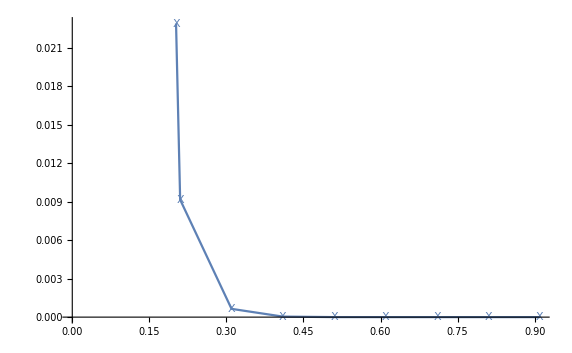

```mathematica
ListPlot[Ivsg2,Joined->True,PlotMarkers->{"X"}]
```

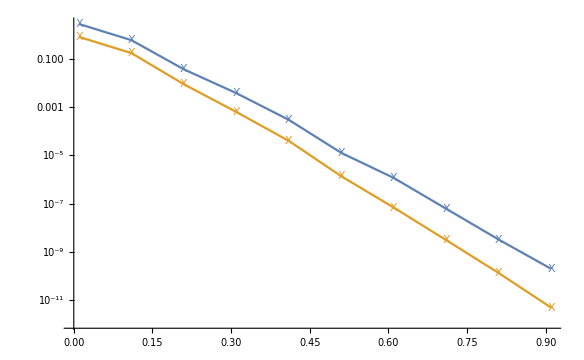

```mathematica
ListLogPlot[{Ivsg,Ivsg2},Joined->True,PlotMarkers->{"X"}]
```

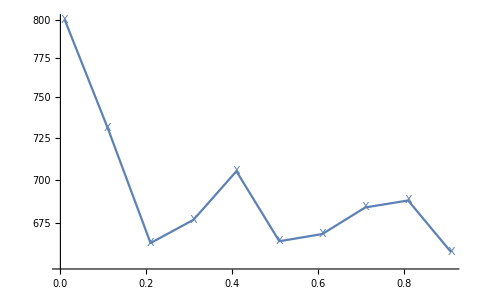

```mathematica
ListLogPlot[charg,Joined->True,PlotMarkers->{"X"}]
```